```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\刘兴瑞\Documents\Visual Studio 2015\Projects\pipe\pipe

```mathematica
top=Flatten[Import["initialtop.csv"]];
bottom=Flatten[Import["initialbottom.csv"]];
```

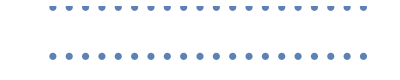

```mathematica
a={};
Do[
a=Append[a,{i,4}];
a=Append[a,{i,1}];
,{i,1,20}]
ListPlot[a,AspectRatio->Automatic,Axes->False]
```

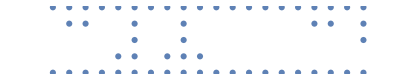

```mathematica
Do[top=ReadList[TemplateApply["top``.txt",{i}]];
bottom=ReadList[TemplateApply["bottom``.txt",{i}]];
a={};
Do[
Do[
a=Append[a,{ii,j}]
,{j,top[[ii]],4}]
Do[
a=Append[a,{ii,k}],{k,0,bottom[[ii]]}]
,{ii,1,Length[top]}]
Print[ListPlot[a,AspectRatio->Automatic,Axes->False]]
,{i,1,1}]
```

```mathematica
b={};
Do[
b=Append[b,{i,top[[i]]}];
b=Append[b,{i,bottom[[i]]}];
,{i,1,Length[top]}]
```

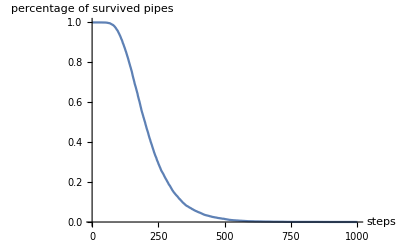

```mathematica
percenp=1-Flatten[Import["percentagepp.csv"]]/10000;
ListLinePlot[percenp,PlotRange->All,AxesLabel->{"steps ","percentage of survived pipes"}]
```

218.227

95.8593

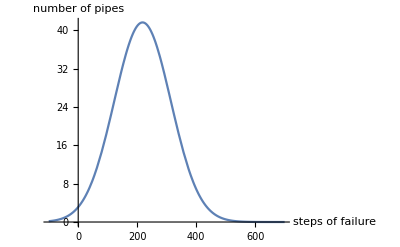

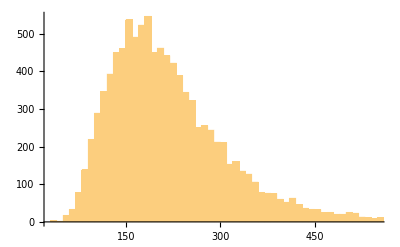

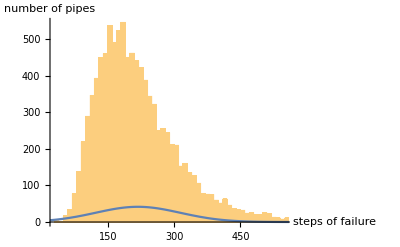

```mathematica
failTimepp=Flatten[Import["fail_timepp.csv"]];
N[Mean[failTimepp]]
N[StandardDeviation[failTimepp]]
disG=Plot[10000*PDF[NormalDistribution[Mean[failTimepp],StandardDeviation[failTimepp]],x],{x,-100,700},PlotRange->All,AxesLabel->{"steps of failure","number of pipes"}]
HG=Histogram[failTimepp,100]
Show[HG,disG,AxesLabel->{"steps of failure","number of pipes"}]
```